# Strava segment analysis

```mathematica
raw= Import[ToFileName[NotebookDirectory[] <> "/data/","segment1.csv"]];
```

```mathematica
colnames = Flatten[Take[raw,1]]
```

{Date,Speed_Kmh,Power_W,Time_M_S}

```mathematica
data = Drop[raw,1];
dates = Map[DateObject,data[[All,1]]]  ;
```

```mathematica
durations = Map[Function[s,With[{l=StringSplit[s,":"]},ToExpression[l⟦1⟧] 60+ToExpression[l⟦2⟧]]],data[[All,4]]];
```

List of {date,duration} paris:

```mathematica
dd=Transpose[{dates, durations}];
```

Plot of all ride durations:

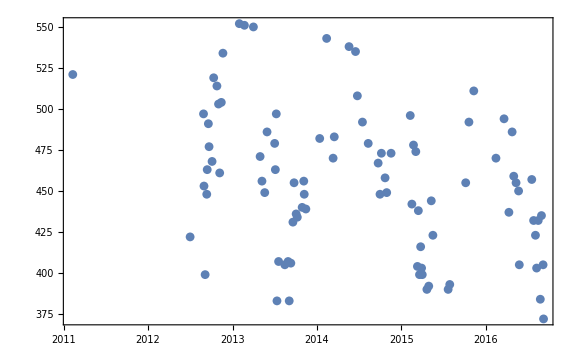

```mathematica
DateListPlot[dd,Joined->False,ImageSize->Large]
```

Let us try to find statistical distribution of all ride durations 2011-2016. We will consider only following distribution models to avoid more exotic ones:

```mathematica
dismodels= {UniformDistribution, NormalDistribution, GammaDistribution};
```

```mathematica
dist=FindDistribution[durations, TargetFunctions->dismodels]
```

MixtureDistribution[{0.386438,0.613562},{NormalDistribution[453.878,27.6987],UniformDistribution[{371.524,551.804}]}]

So the distribution is a mixture of uniform and normal distributions. Let us examine it more closely:

```mathematica
distpdf=PDF[dist,x]
```

Piecewise[{{0.+0.00556584 ⅇ^(-0.000651707 (-453.878+x)^2), x>551.804||x<371.524}, {0.00340339+0.00556584 ⅇ^(-0.000651707 (-453.878+x)^2), True}}]

Let us overlap estimated PDF on top of histogram:

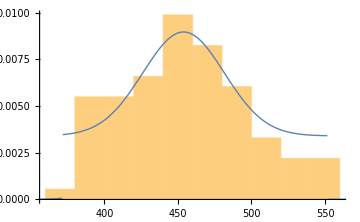

```mathematica
Show[Histogram[durations,10,"ProbabilityDensity",ImageSize->Medium],Plot[distpdf,{x,84.31804732849685,839.6000220767548},ImageSize->Medium,PlotStyle->Thick]]
```

But we need to clear data little more:

1. I know that I started riding regularly in second half of 2012, so data before that is some kind of error
2. There is seems to be a seasonal component which could be explained that I usually ride more cautiously on wet road. We will ignore it for now.
3. Finally, it looks like the results change from year to year depending on my shape, so we will need to look at it by year.

Split by year and drop 2011:

```mathematica
ddbyyear=Drop[SplitBy[Sort[dd],DateList[#1[[1,1]]][[1]] &],1];
durationbyyear=Map[Last,ddbyyear,{2}];
```

Number of samples per year:

```mathematica
Map[Length,durationbyyear]
```

{15,24,15,19,17}

Let us see what distributions fit:

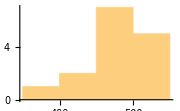
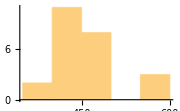
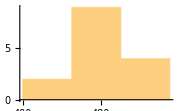
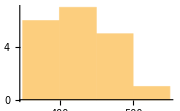
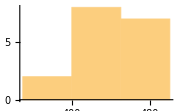
-Graphics- | UniformDistribution[{398.699,534.117}]
-Graphics- | MixtureDistribution[{0.846207,0.153793},{NormalDistribution[437.027,32.7187],NormalDistribution[551.032,0.512426]}]
-Graphics- | MixtureDistribution[{0.76484,0.23516},{NormalDistribution[471.584,17.1954],NormalDistribution[539.796,3.1044]}]
-Graphics- | MixtureDistribution[{0.291808,0.708192},{NormalDistribution[395.176,5.20728],UniformDistribution[{390.117,510.983}]}]
-Graphics- | UniformDistribution[{371.052,493.488}]

```mathematica
Map[{Histogram[#,ImageSize->Small],FindDistribution[#,TargetFunctions->dismodels]} &,durationbyyear]// TableForm
```